# Lebesgue Measure Theory

## Lebesgue 测度的学习笔记

## Chapter 01 测试基本单元

## 零. 基本设置

### 缩放比例

基本的缩放比例是110%，感觉这样的比列看着是最舒服的。

### 快捷键设置

打开选项设置，搜索key。同样的黑体字MenuCommandKey那里修改成自己习惯的数字按键（建议1～9），输入英文状态下的””和数字。比如：”5”

### 具体的定制内容

定制了以下的快捷键：
											-Graphics-

## 一. 数学笔记节

Lebesgue Measure Definition

	基本的Lebesgue定理叙述如下：

Riemann  Integrate Theorem

	让 定义在区间 [a,b]的非负函数，我们要计算f(x)所代表的曲线与x坐标轴的面积，(∫_a)^b f(x)=

Riemann Lemma
	一元积分学中的黎曼引理：若在上绝对可积， 是以为周期的函	数，在上可积，则有：

## 二. 文本节

### 普通文本

这是一段话，用于测试Text环境。法尔科博士说，美国可以发现气球收集的数据是如何被送回中国的。中国可能使用了一个“混合卫星网络”，即利用高空平台将数据中继传输到最靠近的卫星。法尔科博士说，一旦卫星进入安全区域，它就会与地面站或作为控制系统的天线连接。

### code片段

#include<iostream>
using namespace std;
void quickSort(int a[],int,int);
int main()
{
	int array[]={34,65,12,43,67,5,78,10,3,70},k;
	int len=sizeof(array)/sizeof(int);
	cout<<”The original arrayare:”<<endl;
	for(k=0;k<len;k++)
		cout<<array[k]<<”,”;
	cout<<endl;
	quickSort(array,0,len-1);
	cout<<”The sorted arrayare:”<<endl;
	for(k=0;k<len;k++)
		cout<<array[k]<<”,”;
	cout<<endl;
	system(“pause”);
	return 0;
}
 
void quickSort(int s[], int l, int r)
{
	if (l< r)
	{      
		int i = l, j = r, x = s[l];
		while (i < j)
		{
			while(i < j && s[j]>= x) // 从右向左找第一个小于x的数
				j--; 
			if(i < j)
				s[i++] = s[j];
			while(i < j && s[i]< x) // 从左向右找第一个大于等于x的数
				i++; 
			if(i < j)
				s[j--] = s[i];
		}
		s[i] = x;
		quickSort(s, l, i - 1); // 递归调用
		quickSort(s, i + 1, r);
	}
}

## Chapter 02 实际使用

## 三. Code节

### 标准程序代码

```mathematica
Range[1, 30, 2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29}

### 自然语言

Plot[Sin[x], {x, -2*Pi, 2*Pi}]

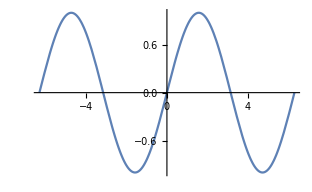

### 普通MMA代码

```mathematica
Integrate[1/(x^5+1),x]
```

1/20 (-2 √(10-2 √5) ArcTan[(1+√5-4 x)/(√(10-2 √5))]+2 √(2 (5+√5)) ArcTan[(-1+√5+4 x)/(√(2 (5+√5)))]+4 Log[1+x]+(-1+√5) Log[1+1/2 (-1+√5) x+x^2]-(1+√5) Log[1-1/2 (1+√5) x+x^2])

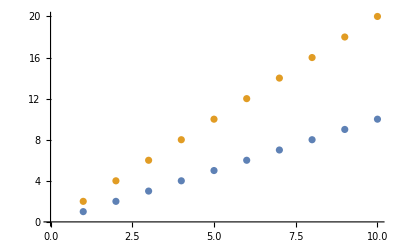

```mathematica
ListPlot[{Range[1, 10], Range[1,10]*2}]
```

## 四.键入laTeX公式

### 1. 安装配置MacTeX

通过插件MaTeX即可简单的键入LaTeX公式，使用如下的语句即可渲染出优美的LaTeX公式。注意MaTeX“”中的内容默认是数学模式。同时注意：首次运行时，需要键入如下的命令才可以使用MaTeX。

>>MaTeX`

1. 安装MaTeX本体

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

2. 配置GhostScrip

```mathematica
<< MaTeX`
```

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

```mathematica
ConfigureMaTeX["Ghostscript" -> "C:\\Users\\PC\\scoop\\apps\\ghostscript\\10.0.0\\bin\\gswin64c.exe"]
```

{pdfLaTeX→C:\texlive\2021\bin\win32\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:\Users\PC\scoop\apps\ghostscript\10.0.0\bin\gswin64c.exe}

### 2. 使用MaTeX

#### 3. MacTeX使用演示

3.1. 运行MaTeX

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x ^ 2"]
```

-Graphics-

3.2. 单个表达式

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k}"]
```

-Graphics-

3.3 单行表达式

```mathematica
MaTeX[{"\\frac{x^2}{\\sqrt{3}}",HoldForm[Integrate[Sin[x],{x,0,2 Pi}]],Expand[(1+x)^5]}]
```

{-Graphics-,-Graphics-,-Graphics-}

3.4 引入常用宏包

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,ctex}"}]
MaTeX["\\color{red}\\sqrt{x}"]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,ctex}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

3.5 支持中文

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,xecjk,tikz}"}](*引入宏包，支持中文等*)
MaTeX["Pi\\longrightarrow \\pi"]
MaTeX["E\\longrightarrow \\mathbf{e}\\text{自然常数}"]
MaTeX["Degree\\longrightarrow \\circ"]
MaTeX["I\\longrightarrow \\mathbf{i}"]
MaTeX["EulerGamma\\longrightarrow \\gamma"]
MaTeX["Infinity\\longrightarrow \\infty"]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,xecjk,tikz}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

注：MaTeX不支持环境(会报错)

```mathematica
MaTeX["
\\begin{align}
&\\alpha +\\beta = \\gamma\\
&\\sum_{i=1}^{\infty}\\frac{1}{i^2}
\\end{align}
"]
```

## External languages

可以使用Python，ruby,Julia,R等各种脚本语言，直接使用即可

### 1. 查找

```mathematica
FindExternalEvaluators["Python"]
```

### 2. 注册特定的版本

```mathematica
(*注册特定的Python版本*)
RegisterExternalEvaluator["Python","C:\\Users\\PC\\AppData\\Local\\Programs\\Python\\Python37-32\\python.exe"]
```

0147371a-a7c6-0679-6cc9-22be99b4a802

### 3. 具体使用

普通使用

1+1

2

使用循环

for i in range(1,10):
	print(i)

2

3

4

5

6

7

8

9

使用 matplotlib 进行绘图并展示

import matplotlib.pyplot as plt
x = [1, 2, 3, 4]
# y坐标轴上点的数值
y = [1, 4, 9, 16]
# 第2步：使用plot绘制线条第1个参数是x的坐标值，第2个参数是y的坐标值
plt.plot(x,y)
# 第3步：显示图形
plt.show()

直接使用 Import 置入pdf文件

```mathematica
Import["C:\\Users\\PC\\Desktop\\Figure_1.pdf"]
```

{-Graphics-}